## 3.029 Spring 2022 Lecture 18 - 04/06/2022

## Surface Energy Anisotropy

Last lecture we investigated the surface tension arising from finite size particles using the Lennard-Jones potential

Today, we’ll investigate the orientational-dependance of surface energy and its implications of on the equilibrium shapes of crystals using the Wulff construction

## Orientational Dependence

We’ve seen in L08 that preferred directions in crystals result in anisotropic physical properties.

Similarly, we expect the surface energy density to be anisotropic

Some orientations will be close-packed and others will have jogs.

In ionic crystals—like NaCl which forms cubic particles—the orientation dependence will be even greater

For a Lennard Jones solid we shouldn’t expect too much anisotropy

The potential is centro-symmetric

Fairly short-ranged

and the hexagonally-closed packed structure is as “isotropic” as crystals can get

Nonetheless, we will recover some anisotropy in the surface energy density

First, let’s get a sense of the anisotropy graphically by “cleaving” our round particle at a particular orientation

We’ll use the uniformly-strained lattice from L17

```mathematica
cleaveParticle[radius_][rotation_]:=With[{round=hexagonalParticle[radius, equilibriumLatticeConstant[radius]hexagonalLatticePoints]},
KeySort[GroupBy[round,Chop[ #.AngleVector[rotation]]<  0&]]//Values
]

cleaveParticleApart[radius_][rotation_]:=MapThread[TranslationTransform[#1AngleVector[rotation]][#2]&,{{1,-1},cleaveParticle[radius][rotation]}]
```

```mathematica
Manipulate[
Graphics[{
particleGraphic[{ljRelaxedEnergyMinimum,ljRelaxedEnergyMaximum}]/@cleaveParticleApart[radius][θ],
{Black,Thick,Dashed,InfiniteLine[{0,0},AngleVector[θ-π/2]]}
},PlotRange->radius{{-1.25,1.25},{-1.25,1.25}}],
{{radius,5,"Particle Radius"},5,15,5/2},{{θ,π/4,"Surface Orientation"},0,2π},Paneled->False]
```

We wish to isolate the orientation-dependent part of the surface energy, by subtracting the bulk energy and surface energy contributions from the round part of the surface

To do so we will compute the average LJ energy for the two cleaved halves and fit it to half the energy model we used earlier, plus a

```mathematica
cleavedParticleEnergyModel=(bulkEnergy (Pi radius^2) + γ (2 Pi radius))/2+2 σ radius+2ρ;
```

```mathematica
cleavedParticles = Association@Table[θ->Association@Table[radius->cleaveParticle[radius][θ],{radius,Range[5,50,5]}],{θ,0,2 Pi,Pi/36}];
```

```mathematica
Clear[anisotropicFit]
anisotropicFit[θ_]:=anisotropicFit[θ]=Block[{data,fit},
data=Table[{r,Mean[(aggregatedLennardJonesEnergies/@cleavedParticles[θ][r])[[All,"Total Energy"]]]},{r,5,50,5}];
fit=FindFit[data,cleavedParticleEnergyModel,{σ,ρ,bulkEnergy,γ},radius];
<|"θ"->θ,"σ"-> σ/.fit,"ρ"-> ρ/.fit|>
]
```

Let’s see how the orientation-dependent part of the surface energy density varies with orientation angle

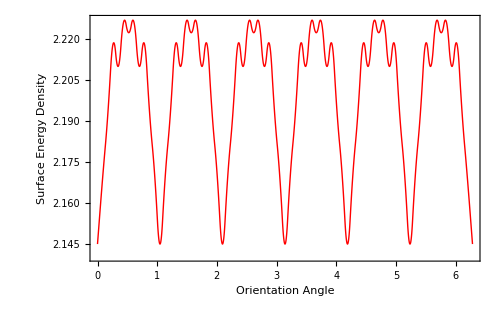

```mathematica
ListLinePlot[anisotropicFit[#][[{"θ","σ"}]]&/@Range[0,2π,π/36],Frame->True,FrameLabel->{"Orientation Angle","Surface Energy Density"},ImageSize->500,LabelStyle->Directive[Black,16],PlotStyle->Directive[Red,Thick],InterpolationOrder->2]
```

As expected, the surface energy density exhibits slight anisotropy, and has six-fold symmetry

Since we’re sweeping the angle from 0-2π to sample all orientations, it’s convenient to plot this in polar coordinates

```mathematica
ListPolarPlot[(anisotropicFit/@Most[Range[0,2π,π/36]])[[All,{"θ","σ"}]],PlotStyle->Directive[PointSize[0.025],Red], PolarGridLines->Automatic, PolarAxes->Automatic,PolarTicks->Automatic,PolarAxesOrigin->{0,2.5},PlotRange->3.25{{-1,1},{-1,1}},ImageSize->500,BaseStyle->Directive[Black,16]]
```

-Graphics-

## Wulff Construction

The Wulff construction is a geometrical construction using tangent-planes proposed, without proof, by Wulff in 1901

To illustrate the construction analytically, we switch to  a parametric form for the surface energy in 2D, whereby we can vary the anisotropy

Where  is the unit vector pointing towards the crystal’s orientation

Since we’re in 2D, we can parametrize  by the angle θ it makes with the {1,0} orientation

```mathematica
squareSurfaceEnergyDensity[α_][θ_]=1+α (Cos[θ]^2 Sin[θ]^2);
squareSurfaceEnergyDensityParametric[α_][θ_]=squareSurfaceEnergyDensity[α][θ]AngleVector[θ];
```

The polar plot below illustrates the particular surface energy density we’ve chosen above, with four-fold symmetry, for various values of anisotropy

```mathematica
Manipulate[
PolarPlot[squareSurfaceEnergyDensity[α][θ],{θ,0,2π},ImageSize->500,PlotRange->2.5{{-1,1},{-1,1}},PolarGridLines->Automatic, PolarAxes->Automatic,PolarTicks->Automatic,BaseStyle->Directive[Black,16],PolarAxesOrigin->{0,2},PlotStyle->Directive[Red,Thick]],
{{α,1/2,"Anistropy"},0,4},Paneled->False,SaveDefinitions->True]
```

The Wulff-construction is geometrically straight-forward

For each point on the surface-energy density polar plot

Plot a tangent plane with some length

The equilibrium crystal shape is then defined as the inner-most envelope of the tangent planes

Before we illustrate a more mathematically-rigorous way to achieve this, we demonstrate the construction below

```mathematica
wulffline[{x_,y_},wulfflength_] := Block[{θ,wulffhalf=wulfflength/2,x1,x2,y1,y2},
θ=ArcTan[x,y];
x1 = x + wulffhalf *Cos[θ + Pi/2];
x2=  x + wulffhalf*Cos[θ - Pi/2];
y1 = y + wulffhalf*Sin[θ + Pi/2];
y2= y + wulffhalf*Sin[θ - Pi/2];
Line[{{x1,y1},{x2,y2}}]
]
```

```mathematica
Manipulate[
With[{f=squareSurfaceEnergyDensityParametric[α]},
Show[Graphics[{Opacity[0.25],Table[wulffline[f[θ],1.5],{θ,0, θMax, 2 Pi/250}]}],ParametricPlot[f[θ],{θ,0,2π},PlotStyle-> {Thickness[0.0075],Red}],PlotRange->2{{-1,1},{-1,1}},ImageSize->500]]
,{{α,1/2,"Anistropy"},0,4},Delimiter,{{θMax,π,"Wulff Construction Extent"},0,2π-2π/250},Paneled->False,SaveDefinitions->True
]
```

## Capillary, ξ - Vector

The surface energy density  we introduced above is only defined on unit vectors

In order to express the tangent-plane construction analytically, it’s convenient to extend the definition to all vectors  by setting

where

This allows us to introduce a new vector-quantity, known as the capillary vector

As defined, the capillary vector achieves the necessary geometric properties of the tangent-plane construction

Namely that the radial component of the capillary vector  is the surface energy density

and that the remaining components defined a vector in the tangent plane

Note: (4) is given in 3D - in 2D the last term is omitted

Let’s construct the capillary vector analytically

```mathematica
squareSurfaceEnergyDensityOrientations[α_][n1_,n2_]=squareSurfaceEnergyDensity[α][θ]/.{Cos[θ]->n1,Sin[θ]->n2};
squareXiVector[α_][θ_]=Block[{p=√(p1^2+p2^2),γp},
γp=p squareSurfaceEnergyDensityOrientations[α][p1/p,p2/p];
FullSimplify[Grad[γp,{p1,p2}]/.{p1->Cos[θ],p2->Sin[θ]},Assumptions->0<θ <2π]
];
```

And plot it over our surface energy-density plot

```mathematica
Manipulate[
Show[
PolarPlot[squareSurfaceEnergyDensity[α][θ],{θ,0,2π},ImageSize->500,PlotRange->2.5{{-1,1},{-1,1}},PolarGridLines->Automatic, PolarAxes->Automatic,PolarTicks->Automatic,PolarAxesOrigin->{0,2},PlotStyle->Directive[Red,Thick]],
ParametricPlot[squareXiVector[α][θ],{θ,0, 2 Pi},PlotStyle->Directive[Blue,Thick]]],
{{α,1/2,"Anistropy"},0,4},Paneled->False,SaveDefinitions->True]
```

Indeed, we can see that the ξ-vector coincides with the equilibrium Wulff shape

which we can verify directly below

```mathematica
Manipulate[
With[{f=squareSurfaceEnergyDensityParametric[α]},
Show[Graphics[{Opacity[0.25],Table[wulffline[f[θ],1.5],{θ,0, 2π-2π/250, 2 π/250}]}],ParametricPlot[squareXiVector[α][θ],{θ,0, 2 Pi},PlotStyle->Directive[Blue,Thick]],PlotRange->2{{-1,1},{-1,1}},ImageSize->500]],
{{α,1/2,"Anistropy"},0,4},Paneled->False,SaveDefinitions->True]
```

### Convexification of 1/γ

What is more, the ξ-vector produces these “ears” of unstable or “forbidden” crystal orientations

We can remove these using a Convex-Hull -based approach

However, we have to work with the reciprocal surface energy density

```mathematica
squareSurfaceEnergyDensityInverseParametric[α_][θ_]=AngleVector[θ]/squareSurfaceEnergyDensity[α][θ];
```

```mathematica
Manipulate[
Show[
PolarPlot[squareSurfaceEnergyDensity[α][θ],{θ,0,2π},ImageSize->500,PlotRange->2.5{{-1,1},{-1,1}},PolarGridLines->Automatic, PolarAxes->Automatic,PolarTicks->Automatic,BaseStyle->Directive[Black,16],PolarAxesOrigin->{0,2},PlotStyle->Directive[Red,Thick]],
ParametricPlot[squareSurfaceEnergyDensityInverseParametric[α][θ],{θ,0,2π},PlotStyle->Directive[RGBColor[0,1/3,0],Thick]]],
{{α,1/2,"Anistropy"},0,4},Paneled->False,SaveDefinitions->True]
```

We can readily convexify the above to return the stable orientations

```mathematica
Manipulate[
Show[
ConvexHullMesh[
squareSurfaceEnergyDensityInverseParametric[α]/@Subdivide[0.,2π,512]
],ParametricPlot[squareSurfaceEnergyDensityInverseParametric[α][θ],{θ,0,2π},PlotStyle->Directive[RGBColor[0,1/3,0],Thick]]
],{{α,1/2,"Anistropy"},0,4},Paneled->False]
```

```mathematica
stableSquareOrientations[α_]:=With[{ch=ConvexHullMesh[squareSurfaceEnergyDensityInverseParametric[α]/@Subdivide[0.,2π,512]]},
Sort[ArcTan@@@MeshCoordinates[ch]]
]
```

And then use the stable orientations to plot the ξ-vector over

```mathematica
Manipulate[
With[{f=squareSurfaceEnergyDensityParametric[α],stable=stableSquareOrientations[α]},
Show[Graphics[{Opacity[0.25],Table[wulffline[f[θ],1.5],{θ,0, 2π-2π/250, 2 π/250}]}],ListLinePlot[squareXiVector[α]/@stable,PlotStyle->Directive[Blue,Thick],InterpolationOrder->2],PlotRange->2{{-1,1},{-1,1}},ImageSize->500]],
{{α,1/2,"Anistropy"},0,4},Paneled->False]
```

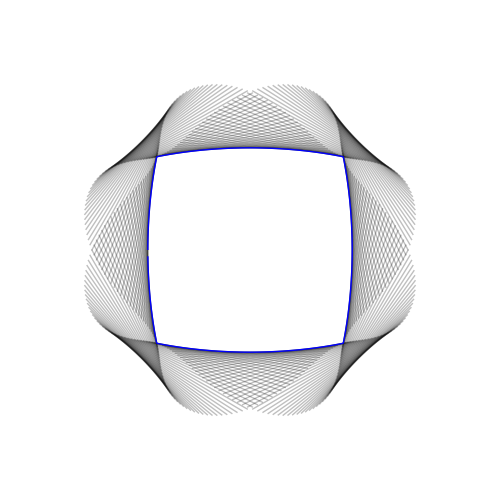

```mathematica
With[{f=squareSurfaceEnergyDensityParametric[2],stable=stableSquareOrientations[2]},
Show[Graphics[{Opacity[0.25],Table[wulffline[f[θ],1.5],{θ,0, 2π-2π/250, 2 π/250}]}],ListLinePlot[squareXiVector[2]/@stable,PlotStyle->Directive[Blue,Thick],InterpolationOrder->2],PlotRange->2{{-1,1},{-1,1}},ImageSize->500]]
```

This approach generalizes readily in 3D

```mathematica
cubicSurfaceEnergyDensityOrientations[α_][n1_,n2_,n3_]=1+α (n1^2 n2^2 n3^2);
cubicXiVector[α_][θ_,ϕ_]=Block[{p=√(p1^2+p2^2+p3^2),γp},
γp=p cubicSurfaceEnergyDensityOrientations[α][p1/p,p2/p,p3/p];
FullSimplify[Grad[γp,{p1,p2,p3}]/.{p1->Cos[ϕ] Sin[θ],p2->Sin[θ] Sin[ϕ],p3->Cos[θ]},Assumptions->0<θ <π&&-π<ϕ<π]
];
```

```mathematica
Multicolumn[ParametricPlot3D[cubicXiVector[#][θ,ϕ],{θ,0,π},{ϕ,-π,π},Boxed->False,Axes->False,PlotPoints->50,ImageSize->150]&/@Range[0,9],5,Appearance->"Horizontal"]//Rasterize
```

-Graphics-

```mathematica
cubicSurfaceEnergyDensity[α_][θ_,ϕ_]=With[{n1=Cos[ϕ] Sin[θ],n2=Sin[θ] Sin[ϕ],n3=Cos[θ]},1+α (n1^2 n2^2 n3^2)];
cubicSurfaceEnergyDensityInverseParametric[α_][θ_,ϕ_]={Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}/cubicSurfaceEnergyDensity[α][θ,ϕ];
```

```mathematica
stableCubicOrientations[α_]:=With[{ch=ConvexHullMesh[cubicSurfaceEnergyDensityInverseParametric[α]@@@Tuples[{Rest@Most@Subdivide[0.,π,128],Subdivide[-π,π,128]}]]},
ToSphericalCoordinates[MeshCoordinates[ch]][[All,2;;]]
]
```

```mathematica
Multicolumn[ListSurfacePlot3D[cubicXiVector[#]@@@stableCubicOrientations[#],Boxed->False,Axes->False,ImageSize->150]&/@Range[0,9],5,Appearance->"Horizontal"]//Rasterize
```

-Graphics-

## Relation to Chemical Potential

Finally, it’s instructive to connect the ξ-vector and the convexification of “forbidden” orientations to the chemical potential and multicomponent phase equilibria

Since we’ve mostly focused on 2D surface energy densities, we’ll illustrate the relation to a binary chemical phase diagram

We define the chemical potentials for both components for the regular-activity model

```mathematica
molarGibbsEnergy["Regular-Activity"][γA_,γB_,ω_,T_,R_:8.314][xB_]=(1-xB) xB ω+R T ((1-xB) Log[γA(1-xB)]+xB Log[γB xB]);

chemicalPotentialA["Regular-Activity"][γA_,γB_,ω_,T_,R_:8.314][xB_]=molarGibbsEnergy["Regular-Activity"][γA,γB,ω,T,R][xB]-xB molarGibbsEnergy["Regular-Activity"][γA,γB,ω,T,R]'[xB];

chemicalPotentialB["Regular-Activity"][γA_,γB_,ω_,T_,R_:8.314][xB_]=molarGibbsEnergy["Regular-Activity"][γA,γB,ω,T,R][xB]+(1-xB) molarGibbsEnergy["Regular-Activity"][γA,γB,ω,T,R]'[xB];
```

And plot the molar gibbs free energy for various temperatures

for a positive interaction parameter

```mathematica
Manipulate[
Plot[molarGibbsEnergy["Regular-Activity"][1,1,5,T][xB],{xB,0,1},Frame->True,FrameStyle->Directive[Black,Thick],ImageSize->500,PlotStyle->Directive[Blue,Thick],LabelStyle->Directive[Black,16],FrameLabel->{"Molar Fraction B, x_B","Molar Gibbs Energy, G̲"}],{{T,1,"Temperature"},0.01,1},Paneled->False]
```

As-well as the two chemical potentials

```mathematica
Manipulate[
Plot[{
chemicalPotentialA["Regular-Activity"][1,1,5,T][xB],
chemicalPotentialB["Regular-Activity"][1,1,5,T][xB]
},{xB,0,1},PlotStyle->{Directive[RGBColor[0,1/3,0],Thick],Directive[Red,Thick]},Frame->True,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[16,Black],ImageSize->500,FrameLabel->{"Molar Fraction B, x_B","Chemical Potential"}],{{T,1,"Temperature"},0.01,1},Paneled->False]
```

If instead of plotting the two chemical potentials separately as a function of composition,

we plot them against each other as we vary the composition we obtain:

```mathematica
Manipulate[
ParametricPlot[{
chemicalPotentialA["Regular-Activity"][1,1,5,T][xB],
chemicalPotentialB["Regular-Activity"][1,1,5,T][xB]
},{xB,0,1},PlotStyle->Directive[Black,Thick],Frame->True,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[16,Black],PlotRange->5{{-1,1},{-1,1}},ImageSize->500,FrameLabel->{"Chemical Potential A, μ_A(x_B)","Chemical Potential B, μ_B(x_B)"}],{{T,1,"Temperature"},0.01,1},Paneled->False]
```

As we lower the temperature, we introduce non-convexities in our Gibbs free energy curve

causing the parametric plot to self-intersect, creating “ears” reminiscent of the ones we saw above

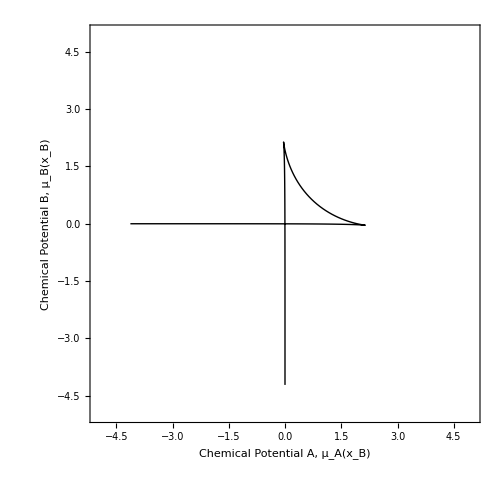

```mathematica
ParametricPlot[{
chemicalPotentialA["Regular-Activity"][1,1,5,0.1][xB],
chemicalPotentialB["Regular-Activity"][1,1,5,0.1][xB]
},{xB,0,1},PlotStyle->Directive[Black,Thick],Frame->True,FrameStyle->Directive[Black,Thick],LabelStyle->Directive[16,Black],PlotRange->5{{-1,1},{-1,1}},ImageSize->500,FrameLabel->{"Chemical Potential A, μ_A(x_B)","Chemical Potential B, μ_B(x_B)"}]
```

Challenge: See if you can make an interactive version of Figs 1 & 2 from this excellent review on the topic: https://link.springer.com/article/10.1007/BF02649804

-Graphics-

## Initialization Functions from L17

```mathematica
lennardJonesEnergies[pts_?MatrixQ]:= Block[
{
distanceMatSquared =DistanceMatrix[pts, DistanceFunction->SquaredEuclideanDistance] + IdentityMatrix[Length[pts]],
distanceMatSixth
},
distanceMatSixth= distanceMatSquared^3;
1/2+1/2 Total[1/distanceMatSixth^2 - 2/distanceMatSixth]
]
```

```mathematica
hexagonalLatticeVectors = {{0,1},{-(√3)/2,1/2}};
hexagonalLatticePoints=With[{range=Ceiling[50/((√3)/2)]},N[Tuples[Range[-range,range],2].hexagonalLatticeVectors]];

hexagonalParticle[radius_,latticePoints_:hexagonalLatticePoints]:=hexagonalParticle[radius,latticePoints]= Select[Norm[#]<radius&][latticePoints]
```

```mathematica
equilibriumLatticeConstant[radius_]=0.9902312792909508+0.009187847342191552/radius^1.1707295148332757;
```

```mathematica
energyColor[{eMin_,eMax_},power_:0.25,cf_:ColorData["DarkRainbow"]][energy_]:= cf[
(Rescale[Clip[energy,{eMin,eMax}],{eMin,eMax},{0,1}])^power]

particleGraphic[{eMin_,eMax_},power_:0.25,cf_:ColorData["DarkRainbow"]][positions_]:= MapThread[{energyColor[{eMin,eMax},power,cf][#1],Disk[#2,1/2]}&,{lennardJonesEnergies[positions],positions}]

{ljRelaxedEnergyMinimum,ljRelaxedEnergyMaximum}=MinMax[lennardJonesEnergies[hexagonalParticle[50,hexagonalLatticePoints equilibriumLatticeConstant[50]]]];
```

```mathematica
aggregatedLennardJonesEnergies[positions_]:=aggregatedLennardJonesEnergies[positions]=With[{es=lennardJonesEnergies[positions]},<|"Energies"->es,"Total Energy"->Total[es],"Average Energy"->Mean[es]|>]
```